```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/johannesk/kette_repo/limit_cycles/src_mathematica/good_fits

```mathematica
LECsNUCL=Import["../LECs_nucl_Joki.dat","Table"][[2;;]];

activeLEC=LECsNUCL[[All,{1,2,3}]];
hbar=197.327053;
Mm=938.92;
m1=2 Mm;m2= Mm;
μ=m1 m2/(m1+m2);
mh2=(2 Mm)/(hbar)^2;
mh2RGM=1/((2.72099 0.529172 137.0373)^2/(938.211+939.505));
Print["ℏ^2/(2 SubscriptBox[m, N]) = ",1/mh2,"=^? ",1/mh2RGM]
```

ℏ^2/(2 SubscriptBox[m, N]) = 20.7355=^? 20.7346

general Gaussian expansion (see so-called ‘’stochastic-variational method’’ of Y. Suzuki & K. Varga):
i,n:=((r̄)_1^2+(r̄)_2^2+(r̄)_3^2)^(n=1)e^(-α_i·(r̄)_1^2-β_i·(r̄)_2^2-γ_i·(r̄)_3^2)

```mathematica
AMA={{2 ("α"+"γ"),2 "γ"},{2 "γ",2 ("β"+"γ")}};
AMAp={{2 ("α'"+"γ'"),2 "γ'"},{2 "γ'",2 ("β'"+"γ'")}};
AM=AMA+AMAp;
iAM=Simplify[Inverse[AM]];
AL21=2 {{"λ",-"λ"},{-"λ","λ"}};
AL22=2 {{4 "λ",2 "λ"},{2 "λ","λ"}};
AL23=2 {{"λ",2 "λ"},{2 "λ",4 "λ"}};
AL31={{4 "λ",2 "λ"},{2 "λ",10 "λ"}};
AL32={{10 "λ",2 "λ"},{2 "λ",4 "λ"}};
AL33={{10 "λ",4 "λ"},{4 "λ",10 "λ"}};
```

```mathematica
Tmat[a_,b_,c_,ap_,bp_,cp_,hbm_]:=
(-hbm) (-2) ((2 π)/(√Det[AM]))^3  ((AMA[[1,1]] AMAp[[1,1]]-1/2 (AMA[[1,1]] AMAp[[1,2]]+AMAp[[1,1]] AMA[[1,2]])+AMA[[1,2]] AMAp[[1,2]]) iAM[[1,1]]+(AMA[[2,2]] AMAp[[2,2]]-1/2 (AMA[[2,2]] AMAp[[1,2]]+AMAp[[2,2]] AMA[[1,2]])+AMA[[1,2]] AMAp[[1,2]]) iAM[[2,2]]+(AMAp[[1,2]] (AMA[[1,1]]+AMA[[2,2]])+AMA[[1,2]] (AMAp[[1,1]]+AMAp[[2,2]])-1/2 (AMA[[1,1]] AMAp[[2,2]]+AMAp[[1,1]] AMA[[2,2]])-AMA[[1,2]] AMAp[[1,2]]) iAM[[1,2]])/.{"α"->a,"β"->b,"γ"->c,"α'"->ap,"β'"->bp,"γ'"->cp}
V2mat[a_,b_,c_,ap_,bp_,cp_,lam_,c0_]:=c0 (((2 π)/(√Det[AM+AL21]))^3+((2 π)/(√Det[AM+AL22]))^3+((2 π)/(√Det[AM+AL23]))^3)/.{"α"->a,"β"->b,"γ"->c,"α'"->ap,"β'"->bp,"γ'"->cp,"λ"->lam}
V3mat[a_,b_,c_,ap_,bp_,cp_,lam_,d1_]:=d1 (((2 π)/(√Det[AM+AL31]))^3+((2 π)/(√Det[AM+AL32]))^3+((2 π)/(√Det[AM+AL33]))^3)/.{"α"->a,"β"->b,"γ"->c,"α'"->ap,"β'"->bp,"γ'"->cp,"λ"->lam}
Nmat[a_,b_,c_,ap_,bp_,cp_]:=(((2 π)/(√Det[AM]))^3)/.{"α"->a,"β"->b,"γ"->c,"α'"->ap,"β'"->bp,"γ'"->cp}

ham[lam_,A_,Ap_,c0_,d1_,e1_]:=V2mat[A[[1]],A[[2]],A[[3]],Ap[[1]],Ap[[2]],Ap[[3]],lam,c0]+V3mat[A[[1]],A[[2]],A[[3]],Ap[[1]],Ap[[2]],Ap[[3]],lam,d1]+Tmat[A[[1]],A[[2]],A[[3]],Ap[[1]],Ap[[2]],Ap[[3]],e1];

norm[A_,Ap_]:=Nmat[A[[1]],A[[2]],A[[3]],Ap[[1]],Ap[[2]],Ap[[3]]];
```

consistency with ‘’hyper-radial expansion’’:

```mathematica
Print["-ℏ/(2 SubscriptBox[m, nucl])∫d(OverBar[r̲]_1,OverBar[r̲]_2)e^(-FractionBox[1, 2] SuperscriptBox[r, T]·A·r)(-2/3((∂^↼)_x_1·OverVector[∂]_x_1+…+(∂^↼)_z_2·OverVector[∂]_z_2)+1/3((∂^↼)_x_1·OverVector[∂]_x_2+…+(∂^↼)_z_1·OverVector[∂]_z_2+(∂^↼)_x_2·OverVector[∂]_x_1+…+(∂^↼)_z_2·OverVector[∂]_z_1))e^(-FractionBox[1, 2] SuperscriptBox[r, T]·SuperscriptBox[A, ']·r) = ",Simplify[Tmat[α,α,α,α',α',α',"ℏ/(2 SubscriptBox[m, N])"]]]
Simplify[V2mat[α,α,α,α',α',α',"λ","C_0"]]
Simplify[V3mat[α,α,α,α',α',α',"λ","D_1"]]
Simplify[Nmat[α,α,α,α',α',α']]
```

-ℏ/(2 SubscriptBox[m, nucl])∫d(OverBar[r̲]_1,OverBar[r̲]_2)e^(-FractionBox[1, 2] SuperscriptBox[r, T]·A·r)(-2/3((∂^↼)_x_1·OverVector[∂]_x_1+…+(∂^↼)_z_2·OverVector[∂]_z_2)+1/3((∂^↼)_x_1·OverVector[∂]_x_2+…+(∂^↼)_z_1·OverVector[∂]_z_2+(∂^↼)_x_2·OverVector[∂]_x_1+…+(∂^↼)_z_2·OverVector[∂]_z_1))e^(-FractionBox[1, 2] SuperscriptBox[r, T]·SuperscriptBox[A, ']·r) = (4 ℏ/(2 SubscriptBox[m, N]) π^3 α α')/(√3 (α+α')^3 √((α+α')^2))

(C_0 π^3)/(√3 ((α+α') (2 λ+α+α'))^(3/2))

1/9 D_1 π^3 ((2 √3)/((3 λ^2+4 λ α+α^2+2 (2 λ+α) α'+(α')^2)^(3/2))+9/((21 λ^2+16 λ α+3 α^2+2 (8 λ+3 α) α'+3 (α')^2)^(3/2)))

π^3/(3 √3 ((α+α')^2)^(3/2))

λ = 6. fm^-1  :  C_0 = -1090.55 MeV    D_1 = 6293.03 MeV

distribution decay constant: 0.9595

distribution decay constant: 0.545764

{-57818.7+0. ⅈ,-53010.1+0. ⅈ,-9049.64+0. ⅈ,-7869.44+0. ⅈ,-7008.25+0. ⅈ,-5502.46+0. ⅈ,-4563.03+7786.26 ⅈ,-4258.65+0. ⅈ,-1936.8+0. ⅈ,-1916.25+1096.25 ⅈ,-1469.56-1813.7 ⅈ,ComplexInfinity}

{-5.44373,-5.39434,-5.35694,-5.3555,-5.35475,-5.34391,-5.31209,-5.216,-5.20643,-4.96827,-4.88584,-4.75863}

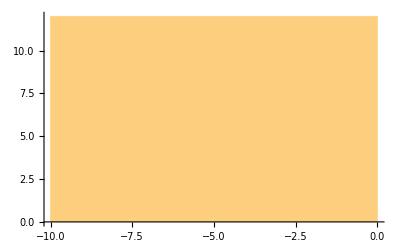

```mathematica
λ=6.00;
C0=1.0 Flatten[Select[activeLEC,#[[1]]==λ&]][[2]];
D1=1.0 Flatten[Select[activeLEC,#[[1]]==λ&]][[3]];
E1=1.0 hbar^2/(2 Mm);
Print["λ = ",λ," fm^-1  :  C_0 = ",C0," MeV    D_1 = ",D1," MeV"]
evlowthreshold=10^-6;
nbrW=12;

gsEresults={};gsEresultsB={};SetSharedVariable[gsEresults,gsEresultsB];

ParallelDo[
dimD=1650;
cent=1.01 (0.95)^nn;
If[nn==1||nn==nbrW,Print["distribution decay constant: ",cent]];
widthsA=Abs[RandomVariate[ErlangDistribution[1,cent+1.0],dimD]];
widthsB=Abs[RandomVariate[ErlangDistribution[2,cent+0.1],dimD]];
widthsG=Abs[RandomVariate[ErlangDistribution[3,cent+0.01],dimD]];
widths=Partition[RandomSample[Join[widthsA,widthsB,widthsG]],3];

hamm=Table[ham[λ^2/4,widths[[i]],widths[[j]],C0,D1,E1],{i,dimD},{j,dimD}];
normm=Table[norm[widths[[i]],widths[[j]]],{i,dimD},{j,dimD}];

normDiag=DiagonalMatrix[1./Sqrt[Diagonal[normm]]];
HamN=(Transpose[normDiag].hamm).normDiag;
NormN=(Transpose[normDiag].normm).normDiag;

esn=Eigensystem[NormN];
evBare=Sort[Eigenvalues[{hamm,normm}],Re[#1]<Re[#2]&];
AppendTo[gsEresultsB,evBare[[1]]];

{μ,transf}=Transpose[Select[Sort[Transpose[esn],#1[[1]]<#2[[1]]&],#[[1]]>evlowthreshold&]];
(*Print[Length[μ]];*)
trafma=(Transpose[transf].DiagonalMatrix[μ^(-1/2)]);
traham=(Transpose[trafma].HamN).trafma;
esh=Eigensystem[traham];
{ϵ,transfe}=Transpose[Sort[Transpose[esh],Re[#1[[1]]]<Re[#2[[1]]]&]];
gsh=transfe[[1,All]];
(*Print["E_0^(bare) = ",Sort[evBare][[1]]];*)
If[Select[ϵ,Re[#]<1.0&]≠{},
AppendTo[gsEresults,{ϵ[[1]],cent}]
(*Print["Dim - Dim_reduced = ",dimD," - ",Length[μ],"     0H0 = ",gsh.traham.gsh," =^! ",ϵ[[1]],"   E_0^(bare) = ",Sort[evBare][[;;4]]]*)
];
,{nn,Range[1,nbrW]}]
Sort[gsEresultsB,Re[#1]<Re[#2]&]
Sort[gsEresults[[All,1]],Re[#1]<Re[#2]&]
Histogram[gsEresults[[All,1]],{10}]
```

```mathematica
gsEresultsB
```

{-3527.+0. ⅈ,-11831.7+0. ⅈ,-1917.12+664.107 ⅈ,-19178.+0. ⅈ,-9215.93+0. ⅈ,-5249.71-5139.35 ⅈ,-115089.+0. ⅈ,-3991.17+0. ⅈ,-2863.78-2127.1 ⅈ,-25046.+0. ⅈ,-23945.1+0. ⅈ,-1500.82+1822.1 ⅈ}

```mathematica
λ=4.00;
C0=1.0 Flatten[Select[activeLEC,#[[1]]==λ&]][[2]];
D1=1.0 Flatten[Select[activeLEC,#[[1]]==λ&]][[3]];

Print["λ = ",λ," fm^-1  :  C_0 = ",C0," MeV    D_1 = ",D1," MeV"]
evlowthreshold=10^-8;
nbrW=12;

gsEresults={};gsEresultsB={};SetSharedVariable[gsEresults,gsEresultsB];

dimD=14;
cent=124.43;
sigmi=12.5;

widthsG={};
ll=0;
While[ll<3 dimD,
widthsG=Join[widthsG ,Select[RandomVariate[NormalDistribution[cent,sigmi],dimD],#>0&]];
ll=Length[widthsG]
];
widths=Partition[widthsG,dimD][[;;3]];

hamm=Table[ham[λ^2/4,widths[[All,i]],widths[[All,j]],C0,D1],{i,dimD},{j,dimD}];
normm=Table[norm[widths[[All,i]],widths[[All,j]]],{i,dimD},{j,dimD}];

normDiag=DiagonalMatrix[1./Sqrt[Diagonal[normm]]];
HamN=(Transpose[normDiag].hamm).normDiag;
NormN=(Transpose[normDiag].normm).normDiag;

NormN//MatrixForm


esn=Eigensystem[NormN];
evBare=Sort[Eigenvalues[{hamm,normm}],Re[#1]<Re[#2]&];
AppendTo[gsEresultsB,evBare[[1]]];

{μ,transf}=Transpose[Select[Sort[Transpose[esn],#1[[1]]<#2[[1]]&],#[[1]]>evlowthreshold&]];
(*Print[Length[μ]];*)
trafma=(Transpose[transf].DiagonalMatrix[μ^(-1/2)]);
traham=(Transpose[trafma].HamN).trafma;
esh=Eigensystem[traham];
{ϵ,transfe}=Transpose[Sort[Transpose[esh],#1[[1]]<#2[[1]]&]];
gsh=transfe[[1,All]];
(*Print["E_0^(bare) = ",Sort[evBare][[1]]];*)
If[Select[ϵ,#<1.0&]≠{},
AppendTo[gsEresults,ϵ[[1]]]
(*Print["Dim - Dim_reduced = ",dimD," - ",Length[μ],"     0H0 = ",gsh.traham.gsh," =^! ",ϵ[[1]],"   E_0^(bare) = ",Sort[evBare][[;;4]]]*)
];

Sort[gsEresultsB,Re[#1]<Re[#2]&]
Sort[gsEresults,#1<#2&]
```

λ = 4. fm^-1  :  C_0 = -505.15 MeV    D_1 = 1395.63 MeV

(1. | 0.989546 | 0.99223 | 0.996657 | 0.990272 | 0.994834 | 0.996355 | 0.995096 | 0.992867 | 0.999315 | 0.998236 | 0.996791 | 0.993393 | 0.994754
0.989546 | 1. | 0.99727 | 0.992835 | 0.998479 | 0.992189 | 0.996067 | 0.991101 | 0.9964 | 0.991256 | 0.990955 | 0.992006 | 0.996735 | 0.985896
0.99223 | 0.99727 | 1. | 0.9975 | 0.999698 | 0.996343 | 0.99879 | 0.997716 | 0.997236 | 0.991259 | 0.996237 | 0.997154 | 0.998388 | 0.988733
0.996657 | 0.992835 | 0.9975 | 1. | 0.995969 | 0.999454 | 0.997853 | 0.998775 | 0.997792 | 0.99471 | 0.99865 | 0.999968 | 0.998474 | 0.988979
0.990272 | 0.998479 | 0.999698 | 0.995969 | 1. | 0.99508 | 0.997872 | 0.995767 | 0.997199 | 0.990009 | 0.994152 | 0.995433 | 0.998169 | 0.986751
0.994834 | 0.992189 | 0.996343 | 0.999454 | 0.99508 | 1. | 0.995704 | 0.996876 | 0.998708 | 0.993014 | 0.996466 | 0.999285 | 0.998891 | 0.984064
0.996355 | 0.996067 | 0.99879 | 0.997853 | 0.997872 | 0.995704 | 1. | 0.998398 | 0.995662 | 0.995565 | 0.998667 | 0.997725 | 0.996935 | 0.994676
0.995096 | 0.991101 | 0.997716 | 0.998775 | 0.995767 | 0.996876 | 0.998398 | 1. | 0.994433 | 0.992295 | 0.999128 | 0.998951 | 0.996027 | 0.99161
0.992867 | 0.9964 | 0.997236 | 0.997792 | 0.997199 | 0.998708 | 0.995662 | 0.994433 | 1. | 0.992655 | 0.993996 | 0.99724 | 0.999826 | 0.982547
0.999315 | 0.991256 | 0.991259 | 0.99471 | 0.990009 | 0.993014 | 0.995565 | 0.992295 | 0.992655 | 1. | 0.996192 | 0.994618 | 0.992818 | 0.994334
0.998236 | 0.990955 | 0.996237 | 0.99865 | 0.994152 | 0.996466 | 0.998667 | 0.999128 | 0.993996 | 0.996192 | 1. | 0.998864 | 0.9953 | 0.994864
0.996791 | 0.992006 | 0.997154 | 0.999968 | 0.995433 | 0.999285 | 0.997725 | 0.998951 | 0.99724 | 0.994618 | 0.998864 | 1. | 0.998007 | 0.989294
0.993393 | 0.996735 | 0.998388 | 0.998474 | 0.998169 | 0.998891 | 0.996935 | 0.996027 | 0.999826 | 0.992818 | 0.9953 | 0.998007 | 1. | 0.984558
0.994754 | 0.985896 | 0.988733 | 0.988979 | 0.986751 | 0.984064 | 0.994676 | 0.99161 | 0.982547 | 0.994334 | 0.994864 | 0.989294 | 0.984558 | 1.)

{9491.86}

{}

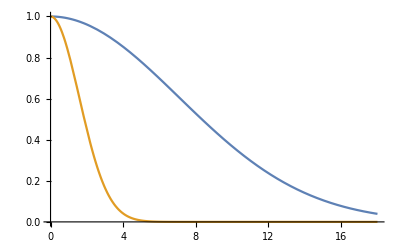

```mathematica
Plot[{Exp[-0.01 x^2],Exp[-0.2 x^2]},{x,0,18},PlotRange->All]
```